```mathematica
cphase={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}};
```

```mathematica
H={{1,1},{1,-1}}/Sqrt[2];
```

```mathematica
S={{1,0},{0,I}};
```

```mathematica
HH=KroneckerProduct[H,H];
```

```mathematica
HS=KroneckerProduct[H,S];
```

```mathematica
SH=KroneckerProduct[S,H];
```

```mathematica
SS=KroneckerProduct[S,S];
```

```mathematica
HI=KroneckerProduct[H,IdentityMatrix[2]];
```

```mathematica
SI=KroneckerProduct[S,IdentityMatrix[2]];
```

```mathematica
IH=KroneckerProduct[IdentityMatrix[2],H];
```

```mathematica
IS=KroneckerProduct[IdentityMatrix[2],S];
```

```mathematica
scaledQ[m1_,m2_]:=MatrixRank[{Flatten@m1,Flatten@m2}]==1
```

```mathematica
phases=Table[Exp[n Pi I /4],{n,0,7}];
```

```mathematica
phaseQ[m1_, m2_]:=Assuming[c∈phases,Reduce[m1==c m2]=!=False]
```

```mathematica
getNewMatrices[matrices_]:=Module[{newMatrices,newWords,keepList,keptMatrices,keptWords},
newMatrices=Flatten[Outer[Dot,matrixGenSet,matrices[[1]],1],1];
newWords=Flatten[Outer[StringJoin,wordGenSet,matrices[[2]],1],1];
keepList=(!AnyTrue[matrices[[1]],Function[M,scaledQ[#,M]],1])&/@newMatrices;
keptMatrices=Pick[newMatrices,keepList];
keptWords=Pick[newWords,keepList];
{keptMatrices,keptWords}=If[Length[keptMatrices]>1,Transpose[Union[Transpose[{keptMatrices,keptWords}],SameTest->Function[{x,y},scaledQ[First[x],First[y]]]]],{keptMatrices,keptWords}];
Return[{Join[keptMatrices,matrices[[1]]],Join[keptWords,matrices[[2]]]}]]
```

```mathematica
count=0;(matrices=NestWhile[(Print[count++];
Union[#~Join~Flatten[Outer[Dot,{HH,HS,SH,SS,cphase},#,1],1]])&,{IdentityMatrix[4]},Length[#2]≠Length[#1]&,2,99])//Length//Timing
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

{190.234,92160}

```mathematica
count=0;(C1matrices=NestWhile[(Print[count++];
Union[#,Flatten[Outer[Dot,{H,S},#,1],1],SameTest->scaledQ])&,{IdentityMatrix[2]},Length[#2]≠Length[#1]&,2,99])//Length//Timing
```

0

1

2

3

4

5

6

{0.140625,24}

```mathematica
matrixGenSet={H,S};
```

```mathematica
wordGenSet={"0","1"};
```

```mathematica
count=0;(C1matrices=NestWhile[(Print[count++];
getNewMatrices[#])&,{matrixGenSet,wordGenSet},Length[#[[1]]]≠24&,2,99]);
```

0

1

2

3

4

5

```mathematica
matrixGenSet={cphase,HI,SI,IH,IS};
```

```mathematica
wordGenSet={"0","1","2","3","4"};
```

```mathematica
count=0;(C2matrices=NestWhile[(Print[count++];
getNewMatrices[#])&,{matrixGenSet,wordGenSet},Length[#[[1]]]≠11520&,2,99]);
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

```mathematica
(*Export["C2matrices_no_phase_duplicates.mx",C2matrices]
```

C2matrices_no_phase_duplicates.mx

```mathematica
Export["C2matrices",C2matrices,"Table"]
```

C2matrices

```mathematica
Export["C2matrices_shortest_words",C2matrices[[2]],"Table"]
```

C2matrices_shortest_words

```mathematica
numZeros=StringCount[C2matrices[[2]],"0"];
```

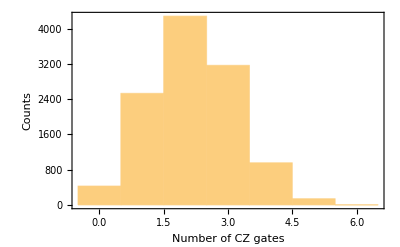

```mathematica
Histogram[numZeros,FrameLabel->{"Number of CZ gates","Counts"},Frame->{True,True,False,False}]
```

```mathematica
N[Mean[numZeros]]
```

2.18533

```mathematica
wordLengths=StringLength@C2matrices[[2]];
```

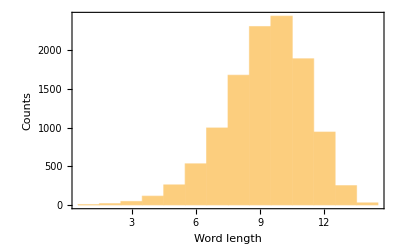

```mathematica
Histogram[wordLengths,FrameLabel->{"Word length","Counts"},Frame->{True,True,False,False}]
```

```mathematica
$ExportFormats
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,C,CDF,Character16,Character32,Character8,Complex128,Complex256,Complex64,CSV,CUR,DAE,DICOM,DIF,DIMACS,DOT,DXF,EMF,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FCS,FITS,FLAC,FLV,FMU,GeoJSON,GIF,Graph6,Graphlet,GraphML,GXL,GZIP,HarwellBoeing,HDF,HDF5,HTML,HTMLFragment,HTTPRequest,HTTPResponse,ICNS,ICO,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JavaProperties,JavaScriptExpression,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LEDA,List,LWO,M4A,MAT,MathML,Maya,MCTT,MGF,MIDI,MO,MOL,MOL2,MP3,MTX,MX,MXNet,NASACDF,NB,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,OFF,OGG,Package,Pajek,PBM,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,POV,PPM,PXR,PythonExpression,QuickTime,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RTF,SCT,SDF,SMA,SMILES,SND,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SVG,SWF,Table,TAR,TerminatedString,TeX,TeXFragment,Text,TGA,TGF,TIFF,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,UUE,VideoFrames,VRML,VTK,WAV,Wave64,WDX,WebP,WLNet,WMF,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XYZ,ZIP,ZPR}